```mathematica
Data={
{500000, 8.33},
{1500000, 8.22},
{2500000, 8.23},
{3500000, 8.20},
{4500000, 8.20},
{5500000, 8.10},
{6500000, 8.07},
{7500000, 8.19},
{8500000, 8.18},
{9500000, 8.07},
{10500000, 8.03},
{11500000, 8.04},
{12500000, 8.01},
{13500000, 7.97},
{14500000, 7.93},
{15500000, 7.84},
{16500000, 7.79},
{17500000, 7.79}};
```

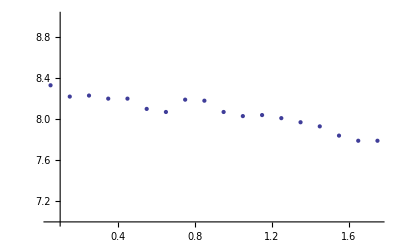

```mathematica
ListPlot[Data,PlotRange->{7,9}]
```

{a→8.31817,b→-4.50893×10^-8,c→3.80095×10^-15,d→-1.76155×10^-22}

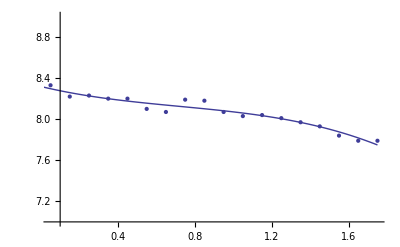

```mathematica
fit=FindFit[Data,a+b x+c x^2+d x^3,{a,b,c,d},x]
Show[
ListPlot[Data,PlotRange->{7,9}],
Plot[Evaluate[a+b x+c x^2+d x^3/.fit],{x,0,17500000}]
]
```